```mathematica
(*TECHNIQUE  OF  VARIATION  OF  PARAMETERS  FOR  SOLVING  INHOMOGENOUS  DIFF.  EQS. *)
```

```mathematica
(*General sol. of inhomogenous diff eq=general sol.of homo. diff eq + particular sol. of inhomogenoes diff eq*)
(*ygen=yh+yp*)

(*1:- yh is obtained by using DSolve [..] command*)
(* yp is obtained through Wronskian Determinant, etc.*)

(*Example Problem*)
(*Solve the inhomogeneous diff eq through the techniques of variation of parameters: y''[x]+xy'[x]+x^2y[x]=2x+1*)

(*Define the inhomogeneous diff eq*)
g[x_]:=2x+1;
inhomoeq=y''[x]+y'[x]+ y[x]==g[x]
homoeq=y''[x]+y'[x]+ y[x]==0
(*Get general sol of homo eq*)
yh=DSolve[homoeq,y[x],x]
yh=y[x]/.yh[[1]]
(*Get linearly independent sols of homo eq from its general sol*)
y1=yh/.{C[1]->1,C[2]->0}
y2=yh/.{C[1]->0,C[2]->1}
(*Get rEADY FOR GETTING PARTICULAR SOL OF INHOMOGENEOUS EQ*)
(*fIRST OF ALL FIND Wronskian Determinant*)
wrons=Det[{{y1,y2},{D[y1,x],D[y2,x]}}]
(*Now get particular sol*)
yp=-y1*Integrate[y2*g[x]/wrons,x]+y2*Integrate[y1*g[x]/wrons,x]
(*Now the general sol of inhomogeneous diff eq*)
ygen=(yh+yp)//Simplify
"The Direct Solution is :"
dirgensol=(y[x]/.(DSolve[inhomoeq,y[x],x])[[1]])//Simplify
```

y[x]+y'[x]+y''[x]==1+2 x

y[x]+y'[x]+y''[x]==0

{{y[x]→ⅇ^(-x/2) C[2] Cos[(√3 x)/2]+ⅇ^(-x/2) C[1] Sin[(√3 x)/2]}}

The Direct Solution is :

-1+2 x+ⅇ^(-x/2) C[2] Cos[(√3 x)/2]+ⅇ^(-x/2) C[1] Sin[(√3 x)/2]

C[1]+x C[2]

1

x

x (-ⅇ^-x+x+x^3/3)-1/4 ⅇ^-x (-4-4 x+2 ⅇ^x x^2+ⅇ^x x^4)+C[1]+x C[2]

{{C[1]→-(6+775 ⅇ^5+6 ⅇ^10)/(12 ⅇ^5),C[2]→-1/(10 ⅇ^5)+ⅇ^5/10}}

-(6+775 ⅇ^5+6 ⅇ^10)/(12 ⅇ^5)+(-1/(10 ⅇ^5)+ⅇ^5/10) x+x (-ⅇ^-x+x+x^3/3)-1/4 ⅇ^-x (-4-4 x+2 ⅇ^x x^2+ⅇ^x x^4)

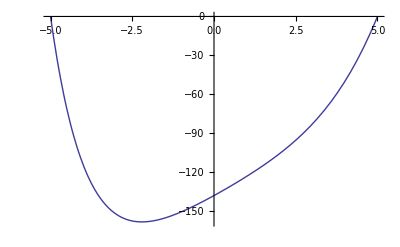

```mathematica
(*Solve the Poisson's(inhomogeneous) diff eq. through the techniques of variation of parameters: ϕ''[x]=-ρ[x]/ϵ,ρ[x]=1+Exp[-x]+x^2  and Plot the General sol for the given Boundary conditions,ϕ[-5]=ϕ[5]=0 *)
homeq=ϕ''[x]==0;
ϵ=1;
ρ[x_]:=1+Exp[-x]+x^2;
inhomeq=ϕ''[x]==-ρ[x]/ϵ;
a=DSolve[homeq,ϕ[x],x];
yk=ϕ[x]/.a[[1]]
Clear[y1,y2,yp,yg]
y1=yk/.{C[1]->1,C[2]->0}
y2=yk/.{C[2]->1,C[1]->0}
Wron=Det[{{y1,y2},{D[y1,x],D[y2,x]}}];
yp=-y1* Integrate[y2*ρ[x]/Wron,x]+y2*Integrate[y1*ρ[x]/Wron,x];
yg=yh+yp
algebeqs={(yg/.x->-5)==0,(yg/.x->5)==0};
con=Solve[algebeqs,{C[1],C[2]}]
yc=yg/.con[[1]]
Plot[yc,{x,-5,5}]
```

```mathematica
f[k_]:=k^2+2k+5; (*If we use delayed assignment,the further values of variable will be delayed. *)
f[1]
k=2;
k=3;
```

8

```mathematica
(*Without delayed assignment,updated value will be used.. *)
```

```mathematica
f[k_]=k^2+2k+5;
f[1]
k=2;
k=3;
```

20